Digital Humanities 1011 - Assignment 11
Name: Dustin Dobransky
Id: 250575030
Date: 2016-02-10
Email: ddobran@uwo.ca

-Graphics-

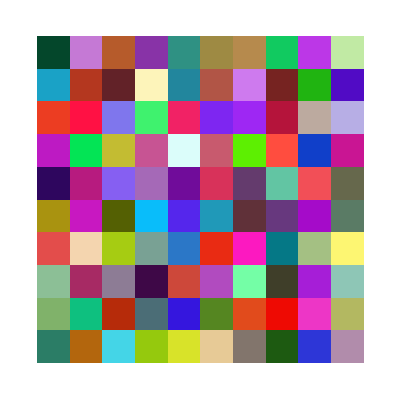

```mathematica
Graphics[
Raster[
Table[{1-Sin[x*Pi/9], 1-Sin[y*Pi/9], Sin[(x+y)*Pi/(9*2)]}
(*Hue[x/10]*),
{x, 0, 9, 1}, 
{y, 0, 9, 1}
]
]
]
Graphics[
Raster[
Table[{RandomReal[],RandomReal[],RandomReal[]}
(*Hue[x/10]*),
{x, 0, 9, 1}, 
{y, 0, 9, 1}
]
]
]
```